# SurfCalc for OGP CCD in-jig measurement data.

PZ Takacs

## SurfCalc OGP_CCDonMF01 ver4.nb

## Extracted from SurfAnal10b

2014.11.21 - ver. 4 Customize for production CCD flatness and height measurement. Include upstemcal offset factor for absolute height correction.
2014.03.30 - ver. 3 Added bad point cleanup iteration to REF points.
2013.05.08 - Added section at end to produce DensityPlot of several files combined by reading in each XLSX absolute height file in the default directory.
2013.04.24 - Rearraged the flatness and outlier threshold trim to output the flatness statistics and trim both the XYX and Z data lists at the same time. Added section to generate a const REF plane if only SUT data. Need to insure slider range is outside the SUT area.
2013.04.10 - Added interruptFlag to skip over Interrupts for faster processing with fixed slider values. Need to change the slider constants as needed.
2013.03.17  Configured to analyze data files from measurements using MF01 metrology fixture. This data file consists of 3 regions - 2 for the 13.000mm gauge block surfaces and 1 for the CCD surface. THe gauge blocks are located off the bottom and top edges of the sensor and are isolated by  y-coordinate limits . A plane surface is fit to the combined point clouds for the gauge blocks (REF). This defines the datum plane for the absolute height measurement, The datum plane is tilted in the OGP coordinate system. The fit function is used to remove the tilt from the CCD surface profile (SUT) so it is referenced to the absolute height of the datum plane.
2013.04.06 - The code was modified to handle the upstems with and without gauge blocks. The raw input can be divided into a SUT and REF region. Outliers are not removed in this nb, except to clean up some points at the margins of the SUT. The CCD and the gauge blocks do not normally have large numbers of outliers. Use the other MF01surface nb if the data has outliers.

```mathematica
Button["Run Initialization first",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

Run Initialization first

## 1. Initialize

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

rijrv_shm16FrontEndObject[LinkObject["rijrv_shm", 3, 1]]16SurfCalc OGP_CCDonMF01 ver4.nb/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data/SurfCalc OGP_CCDonMF01 ver4.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Sat 22 Nov 2014 03:46:13

```mathematica
Off[General::"spell1"]
(*<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
<<"LinearRegression`"*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

## 2. Define statistical functions for profile data.

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

√(-(1. worklist^2)/nbefore^2+(2.+worklist)/nbefore)

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

## Enter full file path here to set working directory:

Enter the filepath for a file in each of the data directories, then copy the desired path into the filepathfull expression.

#### OGP in-jig metrology file paths

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-01/OGP_112-01_01.DAT

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-02/OGP_112-02_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-04/OGP_112-04_02a.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-08/OGP_112-08_02.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-09/OGP_112-09_02.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/113-01/OGP 113-01_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/113-02/OGP 113-02_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/113-03/OGP 113-03_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130314 MF01 in 510 /MF01 130314_03.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130402 MF01 upstem runs/MF01 130403 Xcentralregion_02.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130405 MF01 repeatability/MF01 130405 4blks_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130409 runs/112-02 130409_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130403 MF01 runs/MF01 130403 Xcentralregion_02.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-01 OGP/OGP_112-01_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-02/OGP_112-02_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-03 e2V#046/112-03 1x1fullslowX01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-04 e2V#048/112-04 1x1fullslowX01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-05 e2V#042 mechsamp/112-05 1x1fullslowX01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-06 ITL/112-06_Xbox01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-07 ITL/112-07-Xbox01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-08/112-08_01_run1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/111-01 e2v#021/111-01 1x1fullslowX.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/112-04/OGP_112-04_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/113-02/OGP 113-02_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-08/112-08_01_run1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130507 MF01 runs/MF01 130507 fullboxhires_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-05 e2V#042 mechsamp/130507 runs/OGP_112-05_01gravity.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Sensor&Raft design/Metrology fixtures/MF01 in-jig fixture/MF01 measurements/MF01 fulltop 120711/MF01fulltop01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Sensor&Raft design/Metrology fixtures/MF01 in-jig fixture/MF01 measurements/2 MF01 linescans 120824/MF01linescans.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Sensor&Raft design/Metrology fixtures/MF01 in-jig fixture/MF01 measurements/3 MF01 simple linescans 120828/MF01linescanssimple01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Sensor&Raft design/Metrology fixtures/MF01 in-jig fixture/MF01 measurements/4 MF01 after lapping 120906/MF01_120906_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130507 MF01 runs/MF01 130507 fullboxhires_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/112-05 e2V#042 mechsamp/2013 files/130723 runs/112-05 on MF01 wGBlks.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/114-01 ITL sensor/114-01 140327_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/114-03 ITL sensor/114-03 140328a.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/114-04 ITL sensor/114-04 140328a.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data/141120_01 (110-01).DAT"
```

#### Execute following after setting the proper file path.

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data/141120_01 (110-01).DAT";
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
```

```mathematica
manualcalcFlag=False; (*set for automated analysis*)
```

```mathematica
manualcalcFlag=True; (*to stop automated analysis with default parameters*)
```

### Enter upstemcal offset value here, for later correction of CCD absolute height relative to REF plane.

```mathematica
upstemcal=0;
```

```mathematica
upstemcal=Input["Enter upstemcal offset factor here. Default = 0",upstemcal]
```

0

### Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data

```mathematica
datain=.;datain2=.;datainXYZSR=.;skipnum=.;nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
fnames=FileNames["*.DAT"];Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | 141120_01 (110-01).DAT
2 | 141120_01 test.DAT

#### Pick the OGP file from the list

```mathematica
inst$="OGP"
```

OGP

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
nf=Input["Enter index of file desired",nf]
```

1

```mathematica
fileinfull =fnames[[nf]]
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;
```

141120_01 (110-01).DAT

141120_01 (110-01)

There is no separate REF file, so set filein to fileinS

```mathematica
filein=fileinS;datain=Import[fileinfull,"Data"];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ](* Stop here to execute next expressons individually as needed to clean up data *)
```

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
workdir=filein<>"_files"
```

/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data

141120_01 (110-01)_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

141120_01 (110-01)_files already exists. Using it for output.

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01A e2V ver/MF01A-01 data/141120_01 (110-01)_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
Count[datain,{}] (* Counts the number of blank records in the file*)
```

4593

12

```mathematica
datain2=Select[datain,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
contourPos=Position[datain2,"Contour",2]
Length[contourPos]
```

{{4,1},{314,1},{2019,1},{2290,1},{2595,1},{4300,1}}

6

```mathematica
Length[datain2]
datain2=Select[datain2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
Length[datain2]
```

4581

4567

```mathematica
datain2[[1;;10]]//TableForm;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ]
```

#### All data points are now in one continuous list. All the contours are merged together

#### continue here

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns:

```mathematica
datain3x[[1]]
datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];
datain3x[[1]]
```

{4.2503,-31.5004,-0.001363}

{4.2503,-31.5004,-1.363}

```mathematica
xunit$="mm";yunit$="mm";zunit$="µm"; (*These are now current units*)
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
datainXYZS=datain3x;
datainXYZSR=datainXYZS; (* No REF. Copy surface into SR array. *)
```

```mathematica
skipnum=.;cloudXYZ=.
```

```mathematica
cloudXYZ=datainXYZSR;
Dimensions[cloudXYZ]
```

{4567,3}

Range of raw z-values:

```mathematica
{Min[cloudXYZ[[All,{3}]]],Max[cloudXYZ[[All,{3}]]]}
```

{-31.481,38.792}

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from cloudXYZ based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the cloudXYZ as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
{xmin=Min[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],zmax=Max[zvals],Mean[zvals],StandardDeviation[zvals]}//N
```

{0.596337,41.2039}

{-31.5779,72.9578}

{-31.481,38.792,4.53286,5.81602}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{40.6076,104.536,70.273}

```mathematica
rowscols$="cloud" (*"sparse"*)
```

cloud

Next expression may not contain desired array on first pass. Why???? BEWARE

```mathematica
vp={2,0,1.};
Dynamic[vp];
```

```mathematica
Dimensions[cloudXYZ]
```

{4567,3}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
lpp01=ListPointPlot3D[cloudXYZ,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw data"]
```

-Graphics3D-

```mathematica
Button["Export raw data SUT&REF plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_SUTandREFraw.tiff",lpp01,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export raw data SUT&REF plot

```mathematica
stepinc=1;
imin=xmin;imax=xmax;jmin=ymin;jmax=ymax;
manualcalcFlag
```

False

```mathematica
If[manualcalcFlag,MessageDialog["Set SUT and REF regions with sliders after ABORT"],jmin=-5;jmax=45;MessageDialog["Automatic selection of CCD and gauge block regions"]]  
(*for automated analysis*)  (*Fixed values for CCD and gauge blocks on upstems. Bypass the Manipulate*)
```

rijrv_shm25FrontEndObject[LinkObject["rijrv_shm", 3, 1]]2525

Isolate the CCD region. THis will define the inclusion limits in Y-dir for dividing the data into REF and SUT regions.

```mathematica
Manipulate[Show[lpp01,ImageSize->300,ViewPoint->Dynamic[vp],PlotRange->{{imin,imax},{jmin,jmax},All}]
,{{imin,xmin},xmin,imax,stepinc,Appearance->"Open"},{{imax,xmax},imin,xmax,stepinc,Appearance->"Open"}
,{{jmin,ymin},ymin,jmax,stepinc,Appearance->"Open"},{{jmax,ymax},jmin,ymax,stepinc,Appearance->"Open"},LocalizeVariables->False,SynchronousInitialization->False,SynchronousUpdating->False]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Input["Abort and set sliders now to isolate CCD surface region, then execute next section."]]
```

#### Adjust sliders above to exclude the ref surf regions, then execute these cells.

```mathematica
xyrange={{imin,imax},{jmin,jmax}}
```

{{0.596337,41.2039},{-5,45}}

```mathematica
xminCCD=imin;xmaxCCD=imax;yminCCD=jmin;ymaxCCD=jmax;
```

```mathematica
{{xminCCD,xmaxCCD},{yminCCD,ymaxCCD}}//MatrixForm
```

(0.596337 | 41.2039
-5 | 45)

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Now separate the point cloud into 2 regions: SUT and REF

```mathematica
testS=.;testR=.;SUTdata=.;REFdata=.;
```

```mathematica
testS =Reap[ Do[If[
cloudXYZ[[i]][[1]]<xmaxCCD&& cloudXYZ[[i]][[1]]>xminCCD&&
cloudXYZ[[i]][[2]]<ymaxCCD&& cloudXYZ[[i]][[2]]>yminCCD
,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
SUTdata=Drop[testS,1]//Flatten[#,2]&;
Length[SUTdata]
test=.;
```

3404

```mathematica
splt=ListPointPlot3D[SUTdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw SUT region"]
```

-Graphics3D-

## Now work on Flatness of SUT. Remove tilt with plane fit and trim bad points from residuals.

#### Clean up SUT points, removing outliers. MUST EXECUTE THIS SECTION.

```mathematica
fitbasis={1,x,y};fitidx="1,1";
fitord$=StringTake[ToString[fitbasis],{2,-2}]
```

1, x, y

```mathematica
SUTfit[x_,y_]=Fit[SUTdata,fitbasis,{x,y}]
```

8.05534-0.270356 x+0.131178 y

```mathematica
vp1={2,0,.5};
```

```mathematica
sutfitplt=Plot3D[SUTfit[x,y],{x,xminCCD,xmaxCCD},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]];
```

```mathematica
SUTandFITplane=Show[splt,sutfitplt,PlotRange->All,ViewPoint->Dynamic[vp1],PlotLabel->fileinS<>"\nPlane fit to trimmed SUT points"]
```

-Graphics3D-

```mathematica
Dynamic[vp1]
```

Now trim outliers more than some value away fom the fit plane value.
First subtract plane fit to the full SUT data. NEW VERSION for flatnees stats

```mathematica
SUTresids=Table[{SUTdata[[i,1]],SUTdata[[i,2]],SUTdata[[i,3]]-SUTfit[SUTdata[[i,1]],SUTdata[[i,2]]]},{i,Length[SUTdata]}];
Length[SUTresids]
```

3404

```mathematica
SUTresidsZ=SUTresids[[All,{3}]]//Flatten; (*extract the z-values*)
```

```mathematica
{Mean[SUTresidsZ],Median[SUTresidsZ],StandardDeviation[SUTresidsZ]}
```

{-6.0847×10^-16,-0.870512,4.48724}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

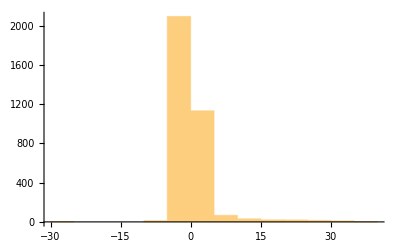

```mathematica
sutflathist=Histogram[SUTresidsZ](*These are the residuals after removing plane fit*)
```

Trim the outliers here.

```mathematica
{threshmin,threshmax}=Input["Enter {min,max} threshold values for trimming bad points.",{threshmin,threshmax}]
```

{-12,35}

Trim both the XYZ and the Z data lists

```mathematica
SUTresidsZtrim=
Drop[
Reap[ 
Do[
If[
SUTdata[[i,3]]-SUTfit[SUTdata[[i,1]],SUTdata[[i,2]]]<threshmax && SUTdata[[i,3]]-SUTfit[SUTdata[[i,1]],SUTdata[[i,2]]]>threshmin,
Sow[SUTdata[[i,3]]-SUTfit[SUTdata[[i,1]],SUTdata[[i,2]] ]]
],
{i,Length[SUTdata]}
]
],
1]//Flatten[#,2]&;
```

```mathematica
SUTresidsZtrim[[1;;10]]
```

{-4.76906,-4.37516,-4.4448,-4.30844,-3.71208,-2.27773,-0.314369,1.95299,4.79635,8.3557}

```mathematica
SUTdatatrim=
Drop[
Reap[
 Do[
If[
SUTdata[[i,3]]-SUTfit[SUTdata[[i,1]],SUTdata[[i,2]]]<threshmax && SUTdata[[i,3]]-SUTfit[SUTdata[[i,1]],SUTdata[[i,2]]]>threshmin,Sow[SUTdata[[i]]]
],
{i,Length[SUTdata]}]
],
1]//Flatten[#,2]&;
```

```mathematica
SUTresidsXYZtrim=Table[{SUTdatatrim[[i,1]],SUTdatatrim[[i,2]],SUTresidsZtrim[[i]]},{i,Length[SUTdatatrim]}];
```

Use these SUT zresids for Flatness statistics. This excludes tilt effects and only looks at intrinsic surface flatness.

```mathematica
maxzF=Max[SUTresidsZtrim];minzF=Min[SUTresidsZtrim];sigmaF=StandardDeviation[SUTresidsZtrim];
zbinF=BinCounts[SUTresidsZtrim,(maxzF-minzF)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeF95=hrange[SUTresidsZtrim,0.025,0.975];
PVrangeF95=hgtrangeF95[[2]]-hgtrangeF95[[1]];
hgtrangeF99=hrange[SUTresidsZtrim,0.005,0.995];PVrangeF99=hgtrangeF99[[2]]-hgtrangeF99[[1]];
sigmaF//NumberForm[#,5]&;
```

```mathematica
sutflatplt=ListPointPlot3D[SUTresidsXYZtrim,PlotRange->All,ViewPoint->Dynamic[vp1],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval","Z [µm]"},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$]
```

-Graphics3D-

```mathematica
Dynamic[vp1]
```

```mathematica
Button["Export SUT Flatness plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTflat.tiff",sutflatplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export SUT Flatness plot

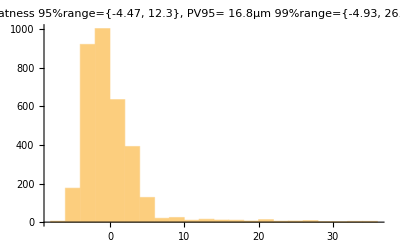

```mathematica
sutflathist=Histogram[SUTresidsZtrim,PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$](*These are the residuals after removing plane fit*)
```

```mathematica
Button["Export SUT Flatness histogram",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTflatHist.tiff",sutflathist,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export SUT Flatness histogram

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

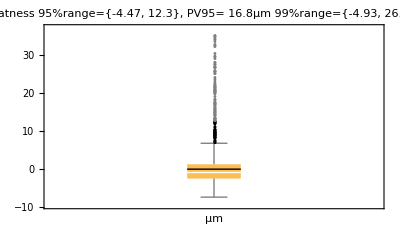

```mathematica
sbwcF=BoxWhiskerChart[SUTresidsZtrim,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export Flatness whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTflatBoxWhsk.tiff",sbwcF,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export Flatness whisker chart file

```mathematica
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.25,0.50,0.75,0.975,0.99,0.995,1.0}];
```

```mathematica
qresF=Quantile[SUTresidsZtrim,quantlist];
```

```mathematica
qtableF=Transpose[{quantlist,qresF}];
%//TableForm
```

1. | 34.8552
0.995 | 26.9251
0.99 | 21.4574
0.975 | 12.3091
0.75 | 1.28015
0.5 | -0.870412
0.25 | -2.46048
0.025 | -4.4651
0.01 | -4.74257
0.005 | -4.92681
0. | -7.32945

```mathematica
Button["Export Flatness Quantile table file",Export[fileinS<>"_"<>sutlen$<>"_SUTflatQuantiles.xlsx",Prepend[qtableF,{fileinS<>", SUT flatness Quantiles"}],"XLSX"]]
```

Export Flatness Quantile table file

```mathematica
Button["Export XYZ flatness height data.",Export[fileinS<>"_"<>sutlen$<>"_SUTflat.xlsx",SUTresidsXYZtrim,"XLSX"]]
```

Export XYZ flatness height data.

```mathematica
strimplt=ListPointPlot3D[SUTdatatrim,PlotRange->All,ViewPoint->Dynamic[vp1],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$]
```

-Graphics3D-

```mathematica
sutlen$=ToString[Length[SUTdatatrim]]
```

3401

```mathematica
Button["Export trimmed SUT region plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTtrim.tiff",strimplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export trimmed SUT region plot

## End of SUT flatness section.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

## Set the SUTdata to the trimmed array and iterate. Continue from here when desired trim is achieved.

```mathematica
SUTdata=SUTdatatrim;
```

## Work on REF region. Do plane fit and toss out bad points. Iterate if necessary.

#### Define REF region: Exclude points outside of central x-region and outside of y-limits.

```mathematica
REFdata=.;testR=.;rplt=.;histresidplt=.;
```

```mathematica
testR =Reap[ Do[If[
(cloudXYZ[[i]][[1]]<xmaxCCD&& cloudXYZ[[i]][[1]]>xminCCD)&&
(cloudXYZ[[i]][[2]]>ymaxCCD|| cloudXYZ[[i]][[2]]<yminCCD)

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
REFdata=Drop[testR,1]//Flatten[#,2]&;
```

```mathematica
Length[REFdata]
```

1161

#### Restart here for REF iteration bad point cleanup

```mathematica
If[Length[REFdata]==0,MessageDialog["Setting REF to const plane"];zSUTconst=Mean[SUTdata[[All,3]]];REFdata=Table[{SUTdata[[i,1]],SUTdata[[i,2]],zSUTconst},{i,Length[SUTdata]}]];
```

```mathematica
zSUTconst=Mean[SUTdata[[All,3]]]
```

5.10853

```mathematica
rplt=ListPointPlot3D[REFdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw REF data"]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
rsplt=.;rsplt=Show[rplt,strimplt]
```

-Graphics3D-

#### Look at REF data

```mathematica
test=.;zREFdata=.;
```

```mathematica
zREFdata=Take[REFdata,All,{3}]//Flatten;
```

```mathematica
maxzR=Max[zREFdata];minzR=Min[zREFdata];sigmaR=StandardDeviation[zREFdata];
zbinR=BinCounts[zREFdata,(maxzR-minzR)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeR99=hrange[zREFdata,0.005,0.995];
PVrangeR99=hgtrangeR99[[2]]-hgtrangeR99[[1]];
sigmaR//NumberForm[#,5]&
```

5.6601

```mathematica
histresidplt=Histogram[zREFdata,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\n99% range="<>ToString[hrange[zREFdata,0.005,0.995]//NumberForm[#,5]&]<>" PV99="<>ToString[PVrangeR99]<>"\nsdev="<>ToString[sigmaR//NumberForm[#,5]&]<>zunit$];
```

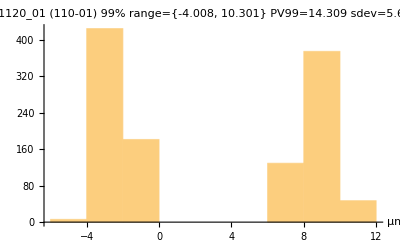

```mathematica
{histresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Now fit a plane surface to the REF points

```mathematica
fitbasisR={1,x,y};fitidxR="1,1";
fitordR$=StringTake[ToString[fitbasisR],{2,-2}]
```

1, x, y

```mathematica
REFfit[x_,y_]=Fit[REFdata,fitbasisR,{x,y}]
```

1.17231-0.0182636 x+0.116078 y

```mathematica
vp1=vp
```

{2,0,1.}

```mathematica
refplt=Plot3D[REFfit[x,y],{x,xminCCD,xmaxCCD},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->200,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
REFcorrected=Table[{REFdata[[i,1]],REFdata[[i,2]],REFdata[[i,3]]-REFfit[REFdata[[i,1]],REFdata[[i,2]]]}
,{i,1,Length[REFdata]}
];
```

```mathematica
reflen$=ToString[Length[REFcorrected]]
```

1161

```mathematica
REFresidsPlt=ListPointPlot3D[REFcorrected,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z[µm]"},PlotLabel->fileinS<>"\nThis shows REF after subt plane fit"]
```

-Graphics3D-

```mathematica
Button["Export REFresids plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_REFresids.tiff",REFresidsPlt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export REFresids plot

```mathematica
zREFresids=Take[REFcorrected,All,{3}]//Flatten;
```

Look at quality of REF plane correction to REF points:

```mathematica
maxzR2=Max[zREFresids];minzR2=Min[zREFresids];sigmaR2=StandardDeviation[zREFresids];
zbinR2=BinCounts[zREFresids,(maxzR2-minzR2)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrange99=hrange[zREFresids,0.005,0.995];
PVrange99=hgtrange99[[2]]-hgtrange99[[1]];
sigmaR2//NumberForm[#,5]&
```

0.85865

```mathematica
histREFresidplt=Histogram[zREFresids,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>" REFresids"<>"\n99%="<>ToString[hrange[zREFresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$];
```

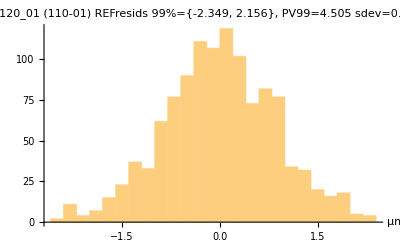

```mathematica
{histREFresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
Button["Export REF resids histogram plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_REFhist.tiff",histREFresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export REF resids histogram plot

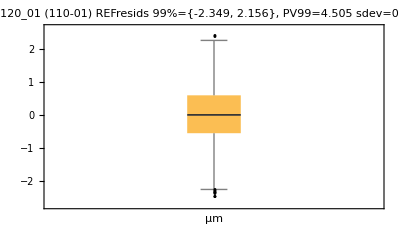

```mathematica
rbwc=BoxWhiskerChart[zREFresids,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>" REFresids"<>"\n99%="<>ToString[hrange[zREFresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export REF box whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_REFboxwhisk.tiff",rbwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export REF box whisker chart file

```mathematica
vp1={2,0,0}
```

```mathematica
SUTandREFplane=Show[rsplt,refplt,PlotRange->All,ViewPoint->Dynamic[vp1],PlotLabel->fileinS<>"\nREF plane fit to trimmed point range"]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export SUT&REF&fitplane plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_S&Rtrim&fitplane.tiff",SUTandREFplane,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export SUT&REF&fitplane plot

#### Iterate REF trim and fit.

Trim off bad points from REF region.

Trim the outliers here.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
threshR=sigmaR2*4
```

3.43461

```mathematica
threshR=Input["Enter ±threshold value for trimming bad REF points.",threshR]
```

3.43461

Trim both the XYZ and the Z data lists

```mathematica
(* Remove the plane from the z-data but not from the XYZ data*)REFresidsZtrim=Drop[Reap[ Do[If[Abs[REFdata[[i,3]]-REFfit[REFdata[[i,1]],REFdata[[i,2]]]]<threshR,Sow[REFdata[[i,3]]-REFfit[REFdata[[i,1]],REFdata[[i,2]]]]],{i,Length[REFdata]}]],1]//Flatten[#,2]&;
```

```mathematica
REFdatatrim=Drop[Reap[ Do[If[Abs[REFdata[[i,3]]-REFfit[REFdata[[i,1]],REFdata[[i,2]]]]<threshR,Sow[REFdata[[i]]]],{i,Length[REFdata]}]],1]//Flatten[#,2]&;
```

```mathematica
REFresidsXYZtrim=Table[{REFdatatrim[[i,1]],REFdatatrim[[i,2]],REFresidsZtrim[[i]]},{i,Length[REFdatatrim]}];
```

```mathematica
refflag=0;
refflag=Input["If need to iterate REF fit, set refflag to 1",refflag]
If[refflag==1,REFdata=REFdatatrim;NotebookLocate["REFdata iterate restart"];Abort[],MessageDialog["Finished with REF"]]
```

0

rijrv_shm37FrontEndObject[LinkObject["rijrv_shm", 3, 1]]3737

## Now do the subtraction of the REF plane from the CCD points. Need to set upstemcal correction factor before execution here.

```mathematica
upstemcal
```

```mathematica
SUTcorrected=Table[{SUTdata[[i,1]],SUTdata[[i,2]],SUTdata[[i,3]]-REFfit[SUTdata[[i,1]],SUTdata[[i,2]]]-upstemcal}
,{i,1,Length[SUTdata]}
];
Length[SUTdata]
```

3401

```mathematica
CCDabshgt=ListPointPlot3D[SUTcorrected,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z[µm]"},PlotLabel->fileinS]
```

-Graphics3D-

```mathematica
zeroplane=Plot3D[0,{x,xmin,xmax},{y,ymin,ymax},PlotStyle->Opacity[0.5]];
```

```mathematica
vp2={2,0,.5};
```

```mathematica
SUTcor3D=Show[CCDabshgt,zeroplane,ViewPoint->Dynamic[vp2],ImageSize->400]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export SUTcor3D plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTabsZ_wZero.tiff",SUTcor3D,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export SUTcor3D plot

```mathematica
zSUTresids=Take[SUTcorrected,All,{3}]//Flatten;
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.25,0.50,0.75,0.975,0.99,0.995,1.0}];
qres=Quantile[zSUTresids,quantlist];
qtable=Transpose[{quantlist,qres}];qtable//TableForm
```

1. | 37.8136
0.995 | 30.0525
0.99 | 24.3224
0.975 | 14.5127
0.75 | 4.45403
0.5 | 2.10756
0.25 | -1.09217
0.025 | -6.53949
0.01 | -7.10079
0.005 | -7.41644
0. | -9.38204

```mathematica
q99range=qres[[8]]-qres[[2]]
```

-36.592

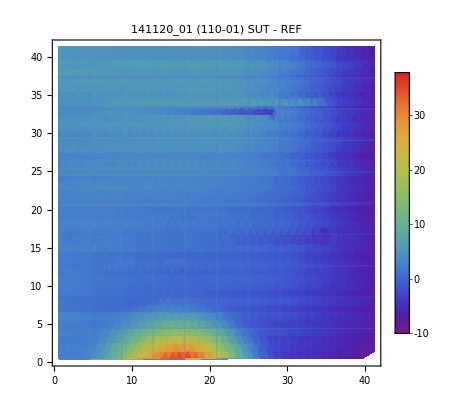

```mathematica
surfdenplt=ListDensityPlot[SUTcorrected,PlotRange->All,ColorFunction->"Rainbow",Mesh->9,PlotLegends->BarLegend[{"Rainbow",{qres[[-1]],qres[[1]]}},LabelStyle->Directive[Bold,FontFamily->"Helvetica"]],PlotLabel->fileinS<>"\nSUT - REF",BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12]]
```

```mathematica
Button["Export Surface Density plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_absSurfDensity.tiff",surfdenplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
```

```mathematica
hgtrangeS95=.;hgtrangeS99=.;PVrangeS95=.;PVrangeS99=. ;
```

```mathematica
maxzS=Max[zSUTresids];minzS=Min[zSUTresids];
meanZcor=Mean[zSUTresids]//Chop;
sigmaS=StandardDeviation[zSUTresids];
zbinS=BinCounts[zSUTresids,(maxzS-minzS)/25];
hgtrangeS95=hrange[zSUTresids,0.025,0.975];PVrangeS95=hgtrangeS95[[2]]-hgtrangeS95[[1]];hgtrangeS99=hrange[zSUTresids,0.005,0.995];
PVrangeS99=hgtrangeS99[[2]]-hgtrangeS99[[1]];
sigmaS//NumberForm[#,{3,3}]&
```

```mathematica
Median[zSUTresids]
```

2.10756

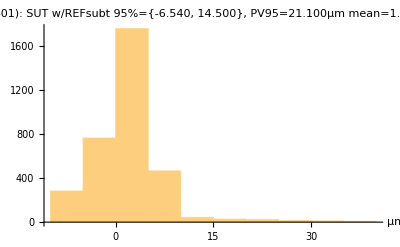

```mathematica
histSUTresidplt=Histogram[zSUTresids,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>": SUT w/REFsubt\n95%="<>ToString[hrange[zSUTresids,0.025,0.975]//NumberForm[#,{3,3}]&]<>", PV95="<>ToString[PVrangeS95//NumberForm[#,{3,3}]&]<>zunit$<>"\nmean="<>ToString[meanZcor//NumberForm[#,{3,3}]&]<>", sigma="<>ToString[sigmaS//NumberForm[#,{3,3}]&]<>zunit$]
```

```mathematica
Button["Export SUT-REF histogram",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTabsZ_Hist.tiff",histSUTresidplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export SUT-REF histogram

```mathematica
ChartElementData["DistributionChart"]
```

{Density,DensityQuantile,FadingQuantile,GlassQuantile,HistogramDensity,LineDensity,PointDensity,Quantile,SmoothDensity}

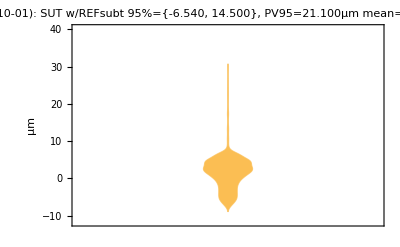

```mathematica
sdensityplt=DistributionChart[zSUTresids,ChartElementFunction->ChartElementData["SmoothDensity"],BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],FrameLabel->{"",zunit$},PlotLabel->fileinS<>": SUT w/REFsubt\n95%="<>ToString[hrange[zSUTresids,0.025,0.975]//NumberForm[#,{3,3}]&]<>", PV95="<>ToString[PVrangeS95//NumberForm[#,{3,3}]&]<>zunit$<>"\nmean="<>ToString[meanZcor//NumberForm[#,{3,3}]&]<>", sigma="<>ToString[sigmaS//NumberForm[#,{3,3}]&]<>zunit$,AxesLabel->{zunit$,zunit$}]
```

```mathematica
quantileMean[{{xmin_,xmax_},{ymin_,ymax_}},data_,metadata_]:=Module[{min,max,lq, uq, median},{min,lq, median, uq, max}=Quantile[data,{0,0.1,0.5,0.9,1}];
{Line[{{xmin, median}, {xmax, median}}]}
]
```

Try to get mean line plotted on snooth density chart:

```mathematica
(*sdensityplt=DistributionChart[zSUTresids,ChartElementFunction->ChartElementData["SmoothDensity",ChartElementFunction->quantileMean],BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],FrameLabel->{"",zunit$},PlotLabel->fileinS<>": SUT w/REFsubt\n95%="<>ToString[hrange[zSUTresids,0.025,0.975]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrangeS99//NumberForm[#,3]&]<>"\nmean="<>ToString[meanZcor//NumberForm[#,3]&]<>", sigma="<>ToString[sigmaS//NumberForm[#,3]&]<>zunit$,AxesLabel->{zunit$,zunit$}] *)
```

```mathematica
Button["Export smooth density chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTabsZ_density.tiff",sdensityplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export smooth density chart file

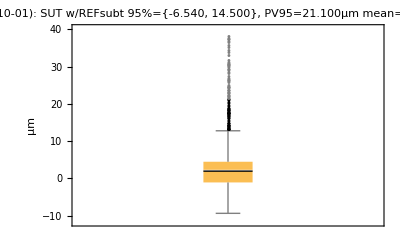

```mathematica
bwc=BoxWhiskerChart[zSUTresids,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],FrameLabel->{"",zunit$},PlotLabel->fileinS<>": SUT w/REFsubt\n95%="<>ToString[hrange[zSUTresids,0.025,0.975]//NumberForm[#,{3,3}]&]<>", PV95="<>ToString[PVrangeS95//NumberForm[#,{3,3}]&]<>zunit$<>"\nmean="<>ToString[meanZcor//NumberForm[#,{3,3}]&]<>", sigma="<>ToString[sigmaS//NumberForm[#,{3,3}]&]<>zunit$,AxesLabel->{zunit$,zunit$}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export box whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>sutlen$<>"_SUTabsZ_whisker.tiff",bwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

```mathematica
Button["Export Quantile table file",Export[fileinS<>"_"<>sutlen$<>"_SUTabsZ_Quantiles.xlsx",Prepend[qtable,{fileinS<>", Quantiles"}],"XLSX"]]
```

Output the detrended data triplets

ADD HEADER info to output file. Output in Excel format. This format drops off the brackets upon opening in Excel. Ordinary text file imports with brackets showing.
Can’t make the header info appear on separate lines at start of Excel file.

```mathematica
SUTout=Prepend[SUTcorrected,{fileinS,DateString[],{"X(mm)","Y(mm)","Z(micron)"}}];
SUTout[[1;;5]];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export absolute height data relative to gauge block datum.",Export[fileinS<>"_"<>sutlen$<>"_SUTcorrAbsHgt.xlsx",SUTout,"XLSX"]]
```

Export absolute height data relative to gauge block datum.

## Remove obvious outliers from SUTdata if necessary. Skip this section if not necessary.

```mathematica
{minS,medianS,maxS,stddevS}=Operate[{Min[#],Median[#],Max[#],StandardDeviation[#]}&,SUTdata[[All,{3}]]//Flatten,0]
```

{-8.773,4.983,38.756,5.66993}

```mathematica
MedianDeviation[SUTdata[[All,{3}]]//Flatten]
```

3.488

```mathematica
threshS=3*(Min[maxS-medianS,medianS-minS])(*Set trim threshold to 3 times the smaller deviation from the median*)
```

41.268

```mathematica
threshS=2*stddevS(*Set trim threshold to 3 times the smaller deviation from the median*)
```

```mathematica
Length[SUTdata]
```

3401

```mathematica
testS=.;
testS =Reap[ Do[If[
Abs[SUTdata[[i]][[3]]-medianS]<threshS
,Sow[SUTdata[[i]]]],{i,Length[SUTdata]}]];
testS=Drop[testS,1]//Flatten[#,2]&;
```

```mathematica
Length[testS]
```

3401

```mathematica
If[Length[testS]==Length[SUTdata],MessageDialog["No points were trimmed from SUTdata"]]
```

rijrv_shm42FrontEndObject[LinkObject["rijrv_shm", 3, 1]]4242

```mathematica
If[Length[testS]>0,SUTdata=testS,MessageDialog["Problem with trimming SUTdata"]];(*Abort if problem trimming SUT data*)
```

```mathematica
testS=.;
```

```mathematica
splt=ListPointPlot3D[SUTdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nSUT-outliers"]
```

-Graphics3D-

## Plot combined DistributionChart for several height residual data files.

#### Default directory is same as set earlier.

First list the desired XLSX files using the wild card. THen edit the picklist to select the desired files. THe result is

```mathematica
upstemoffset=4.49;
```

```mathematica
Input["Enter upstem offset value that gets subtracted from the input height data. This must correspond to the value measured during the initial calibration run on the day of the measurements.",upstemoffset]
```

4.49

```mathematica
fnames1=FileNames["*SUTcorrAbsHgt.xlsx"]
```

{}

```mathematica
Table[{i,fnames1[[i]]},{i,Length[fnames1]}]//TableForm
```

{}

Create picklist here:

```mathematica
picklist={1,2,4,5,7,8};
```

```mathematica
picklist={1,2,4,5,6,7,8,9,10,11}
```

```mathematica
data2=Table[Drop[(Import[fnames1[[i]],"Data"][[1,All,{3}]]//Flatten)-upstemoffset,1]
,{i,picklist}];
```

```mathematica
Dimensions[data2[[]]]
```

```mathematica
Short[data2,10]
```

Now generate qlist with 2 significant digits. Then convert to strings and replace the comma separators with newlines within each row. This preserves the list structure but makes the string list print out vertically to use as annotation for the x-axis.

```mathematica
quantlist=Reverse[{0.0,0.005,0.025,0.50,0.975,0.995,1.0}];
```

```mathematica
qlist=Map[Quantile[#,quantlist]&,data2]
```

```mathematica
qrows=Map[NumberForm[#,{4,2}]&,qlist]
```

```mathematica
qrows2=Map[StringReplace[ToString[#],{","->"\n","{"->"","}"->""}]&,qrows];
```

```mathematica
Dimensions[qrows2]
```

Compute list of median values.

```mathematica
medlist=Map[NumberForm[Median[#],3]&,data2]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
combinedplt=DistributionChart[data2,ChartLabels->Placed[{medlist,qrows2},{Center,Axis}],BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],FrameLabel->{"",zunit$},AxesLabel->{zunit$,zunit$},ImageSize->500,PlotLabel->"Absolute height relative to 13.000mm\nCorrected for upstem offset of "<>ToString[upstemoffset]<>zunit$]
```

Keep existing value for plot neame if it already exists. Otherwise, set it to a default NoName.

```mathematica
If[ValueQ[comboplt],Null,comboplt="NoName"]
```

```mathematica
comboplt=InputString["Enter file name for output of the plot file.",comboplt]
```

```mathematica
Button["Export combined result plot",Export[comboplt<>"_comboDensityPlot.tiff",combinedplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```